```mathematica
mydata=OpenRead[ "/Users/your_account/test.dat",BinaryFormat->True]
```

```mathematica
BinaryRead[mydata,"Integer32"];
t=BinaryRead[mydata,"Real64"];
BinaryRead[mydata,"Integer32"];
Print[t]
```

2.00067

```mathematica
BinaryRead[mydata,"Integer32"];
ix=BinaryRead[mydata,"Integer32"];
BinaryRead[mydata,"Integer32"];Print[ix]
```

202

```mathematica
BinaryRead[mydata,"Integer32"];
jx=BinaryRead[mydata,"Integer32"];
BinaryRead[mydata,"Integer32"];Print[jx]
```

202

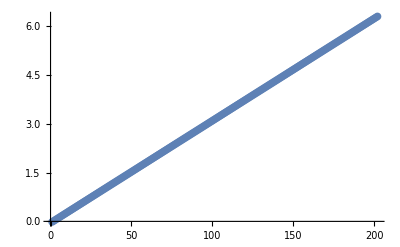

```mathematica
BinaryRead[mydata,"Integer32"];
x=BinaryReadList[mydata,"Real64", ix];  
BinaryRead[mydata,"Integer32"];
ListPlot[x]
```

```mathematica
BinaryRead[mydata,"Integer32"];
y=BinaryReadList[mydata,"Real64", jx];
 BinaryRead[mydata,"Integer32"];
```

```mathematica
ijx=ix*jx
```

40804

```mathematica
BinaryRead[mydata,"Integer32"];mymx=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];mymy=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];mymz=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myen=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myro=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];mybx=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myby=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];mybz=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myps=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myvx=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myvy=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];myvz=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];BinaryRead[mydata,"Integer32"];mypr=BinaryReadList[mydata,"Real64",ijx];BinaryRead[mydata,"Integer32"];
```

```mathematica
Close[mydata]
```

```mathematica
ListContourPlot[ArrayReshape[mypr,{ix,jx}]]
```

```mathematica
ListDensityPlot[ArrayReshape[mypr,{ix,jx}]]
```

```mathematica
ListPlot3D[ArrayReshape[mypr,{ix,jx}]]
```